#### Plotting an Emission Line Spectrum from SDSS data

This example shows how you can work with FITS data easily and generate plots from the raw data.

Download a sample FITS file from the Sloan Digital Sky Survey (SDSS) data server and save it to a local file:

```mathematica
file=URLDownload["https://data.sdss.org/sas/dr16/sdss/spectro/redux/26/spectra/1323/spec-1323-52797-0012.fits","~/example.fits"];
```

Examine the general information for this dataset. Note how the date, right ascension, and declination are included:

```mathematica
information=Dataset[Import[file,{"FITS","MetaInformation"}]][1,"GENERAL INFORMATION"]
```

The FITS data contains multiple spectra. Let’s import one from the second header data unit (HDU):

```mathematica
spectrum=Import[file,{"FITS","Data",2}];
```

Also get the headers for this data:

```mathematica
headers=Import[file,{"FITS","TableHeaders",2}]
```

{flux,loglam,ivar,and_mask,or_mask,wdisp,sky,model}

Construct a dataset from this data, using the header names:

```mathematica
ds=Dataset[AssociationThread[headers->Transpose[spectrum]]]
```

Convert the “loglam” (the log_10 wavelengths) column to wavelengths in Angstroms:

```mathematica
wavelengths=QuantityArray[Normal[10^ds["loglam"]],"Angstroms"]
```

QuantityArray[…]

Compute the measured flux:

```mathematica
flux=QuantityArray[Normal[10^-17*ds["flux"]],"Ergs"/("Centimeters"^2 "Seconds" "Angstroms")]
```

QuantityArray[…]

The conversion factor comes from the metadata information:

```mathematica
information["BUNIT",1]
```

1E-17 erg/cm^2/s/Ang

Plot the wavelengths versus the flux:

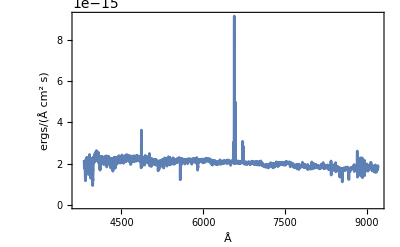

```mathematica
ListLinePlot[Transpose[{wavelengths,flux}],
PlotRange->All,Frame->True,
FrameLabel->{QuantityForm["Angstroms","Abbreviation"],QuantityForm["Ergs"/("Centimeters"^2 "Seconds" "Angstroms"),"Abbreviation"]}]
```